```mathematica
ClearAll["Global`*"]
```

# Some functions

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptionsBasic={PlotRange->Full,PlotLegends->Automatic,Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};
densityPlotOptionstime={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"t","T_f"},Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};
densityPlotOptionsParam={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"T_f","\\Omega"},Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\Omega","\\Delta"},Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,FrameLabel->MaTeX/@{"\\Omega","\\Delta"},Axes->False};getTimeFromSolve[list_]:=list[[1,2,2,1,1,2]]
PlotSol[sol_,col_:"Green"]:=ParametricPlot[
{a[t],b[t]}/.sol,{t,0,getTimeFromSolve[sol]}
,PlotRange->All,Frame->True,Evaluate@plotOptions,PlotStyle->ToExpression@col,AspectRatio->1]
```

```mathematica
dim=2;
H[Ω_,Δ_]:={{Ω,Δ},{Δ,-Ω}}
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors,enNonSort,eigNonSort},
{enNonSort,eigNonSort}=Eigensystem[H[λ,χ]];
{energies,eigenvectors}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
Fidelity[bra_,ket_]:=Norm[Conjugate[bra].ket]^2
eigenvectorsSorted[Ω_,Δ_,t_]:=Module[{H,enNonSort,eigNonSort,energies,eig},
H={{Ω,Δ},{Δ,-Ω}};
{enNonSort,eigNonSort}=Eigensystem[H];
{energies,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
Map[Normalize,eig]
]
eigSortedHfunction[H_]:=Module[{enNonSort,eigNonSort,energies,eig},
{enNonSort,eigNonSort}=Eigensystem[H];
{energies,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
Map[Normalize,eig]
]
```

# Define driving

## Defining different drivings

### Geodesic

```mathematica
Ωscale=10;
θ[t_]:=π t 
Ω[t_]:=-Ωscale Cos@θ[t]
Δ[t_]:=Ωscale Sin@θ[t]
```

### Linear

```mathematica
Ωscale=10;
Ωl[t_]:=0.3
Δl[t_]:=Ωscale (-1+2 t)
```

# Parametric space visualizations

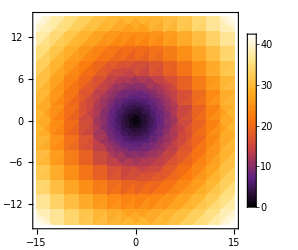

```mathematica
enPlot=DensityPlot[Differences[Eigenvalues@H[Ω,Δ]][[1]],{Ω,-15,15},{Δ,-15,15},Evaluate@densityPlotOptions,ImageSize->250]
```

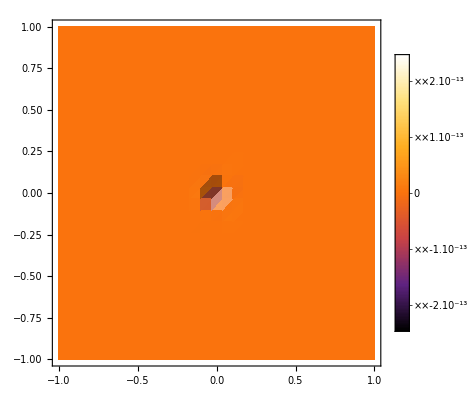

```mathematica
DensityPlot[Det@g[Ω,Δ],{Ω,-1,1},{Δ,-1,1},Evaluate@densityPlotOptions,PlotPoints->30,PerformanceGoal->"Quality",Exclusions->None]
```

### How does it look like?

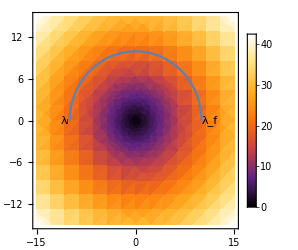

```mathematica
drivingFig=Show[{
enPlot,
ParametricPlot[{Ω[t],Δ[t]},{t,0,1}],
(*ParametricPlot[{Ωl[t],Δl[t]},{t,0,1},PlotStyle->Dashed],*)
Graphics[Text["λ_i",{Ω[0],Δ[0]},{1.5,0}]],
Graphics[Text["λ_f",{Ω[1],Δ[1]},{-1.5,0}]]
}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/driving.pdf",drivingFig,"AllowRasterization"->True,ImageResolution->800];
```

# Numerics

Functions input are two 1 - parametric functions of time, defining the driving, and t as time, or Tf as final time .
Output is function value and norm of vector, for numerical precision control.

```mathematica
FidPlot[Ω1_,Δ1_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,sol,t},
Ω[t_]:=Ω1[t/Tf];
Δ[t_]:=Δ1[t/Tf];
H[t_]:={{Ω[t],Δ[t]},{Δ[t],-Ω[t]}};
eig[t_]:=eigenvectorsSorted[Ω[t],Δ[t],t];
Ψ[t_]={a[t],b[t]};
sol=NDSolve[{I Ψ'[t]==H[t].Ψ[t],Ψ[0]=={1,0}},Ψ[t],{t,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
{Plot[1-Fidelity[Flatten[Ψ[t]/.sol],eig[t][[1]]],{t,0,Tf},Evaluate@font,Frame->True,FrameLabel->{"t","F"},ImageSize->Medium],
Plot[Norm[Evaluate[Ψ[t]/.sol]],{t,0,Tf},Evaluate@font,Frame->True,FrameLabel->{"t","|Ψ(t)|"},ImageSize->Medium]}
]
FidFinal[Ω1_,Δ1_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,sol,t},
Ω[t_]:=Ω1[t/Tf];
Δ[t_]:=Δ1[t/Tf];
H[t_]:={{Ω[t],Δ[t]},{Δ[t],-Ω[t]}};
eig[t_]:=eigenvectorsSorted[Ω[t],Δ[t],t];
Ψ[t_]={a[t],b[t]};
sol=NDSolve[{I Ψ'[t]==H[t].Ψ[t],Ψ[0]=={1,0}},Ψ[t],{t,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
Fidelity[Flatten[Ψ[t]/.sol]/.t->Tf,eig[Tf][[1]]]

]
```

## Testing numerical results on linear driving (to compare with Felipes results)

### Fidelity in time = probability of excitation, with error

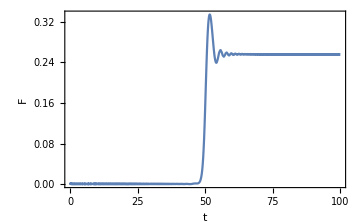
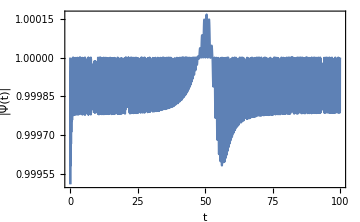

```mathematica
FidPlot[Ωl,Δl,100]
```

### Probability of non - excitation

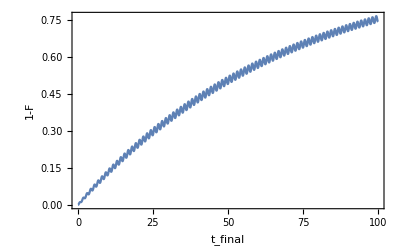

```mathematica
Plot[1-FidFinal[Ωl,Δl,tfinal],{tfinal,0.01,100},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

### Felipe-like result

```mathematica
Plot[FidFinal[Ωl,Δl,tfinal],{tfinal,10^4,10^6},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->5,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

$Aborted

### Result from the paper - fidelity dependence on Tf

```mathematica
(*Plot[FidFinal[Ωl,Δl,1/trev],{trev,0.001,1},PlotRange->All,PlotPoints->5,ScalingFunctions->"Log",Evaluate@font,Frame->True,FrameLabel->{"1/t_final","-log(F)"}]*)
```

## numerical results: Geodesic driving (half-sphere)

### Fidelity in time with error

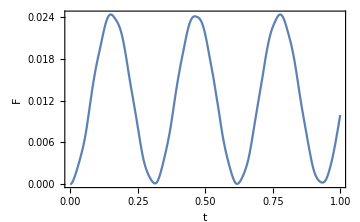
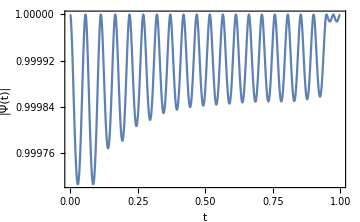

```mathematica
FidPlot[Ω,Δ,1]
```

### Probability of non - excitation

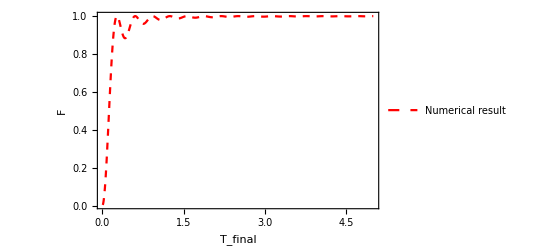

```mathematica
infidelityTfPlotNumerical=Plot[FidFinal[Ω,Δ,tfinal],{tfinal,0.01,5},PlotRange->All,PlotPoints->50,Evaluate@font,Frame->True,PlotStyle->{Dashed,Red},FrameLabel->{"T_final","F"},PlotLegends->Placed[{"Numerical result"},{0.75,0.25}]]
```

### Infidelity dependence on Tf - loglog

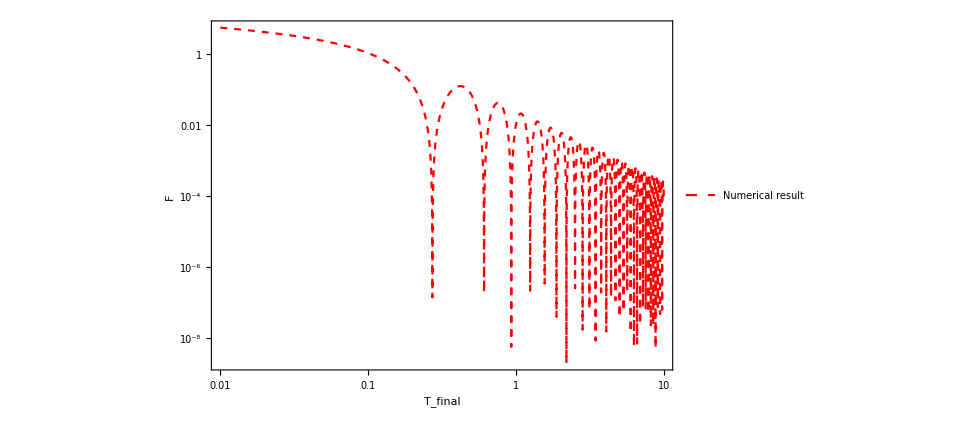

```mathematica
infidelityTfPlotLogNumerical=Plot[-Log@FidFinal[Ω,Δ,tfinal],{tfinal,0.01,10},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->150,Evaluate@font,Frame->True,FrameLabel->{"T_final","F"},PlotStyle->{Dashed,Red},PlotLegends->Placed[{"Numerical result"},{0.15,0.15}]]
```

# Geodesical driving

```mathematica
σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
Hpurple[t_,Tf_]:={-s Cos[ω[Tf] t],0,s Sin[ω[Tf] t]}.σ
Hblue[t_,Tf_]:={{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}
```

```mathematica
Hpurple[t,Tf]//MatrixForm
```

(10 Sin[(π t)/Tf] | -10 Cos[(π t)/Tf]
-10 Cos[(π t)/Tf] | -10 Sin[(π t)/Tf])

## Some calculations along the way

```mathematica
Hc[t_]:=d[t,10,100].σ
```

```mathematica
HH={-s Cos[ω t],0,s Sin[ω t]}.σ
MatrixExp[I ω t σ[[2]]/2].HH.MatrixExp[-I ω t σ[[2]]/2]//FullSimplify//MatrixForm
```

{{s Sin[t ω],-s Cos[t ω]},{-s Cos[t ω],-s Sin[t ω]}}

(0 | -s
-s | 0)

```mathematica
HH//MatrixForm
```

(s Sin[t ω] | -s Cos[t ω]
-s Cos[t ω] | -s Sin[t ω])

```mathematica
Eigensystem[HH]
```

{{-s,s},{{Sec[t ω]-Tan[t ω],1},{-Sec[t ω]-Tan[t ω],1}}}

```mathematica
Hblue={{-ω/2,-s},{-s,ω/2}};
Ublue=MatrixExp[-I Hblue t]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]-(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
U=MatrixExp[-I ω t σ[[2]]/2].Ublue.MatrixExp[I ω t σ[[2]]/2]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ (ω Cos[t ω]-2 s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ (-ω Cos[t ω]+2 s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
U//MatrixForm
```

```mathematica
({{Cos[q t]+(ⅈ (ω Cos[t ω]-2 s Sin[t ω]) Sin[qt])/(2q), (ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[qt])/(2q)}, {(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[qt])/(2q), Cos[qt]+(ⅈ (-ω Cos[t ω]+2 s Sin[t ω]) Sin[qt])/(2q)}})
```

```mathematica
N@Det[Ublue/.{t->1,s->10,ω->10}]
```

1.

```mathematica
N@Norm[Ublue.{1,0}/.{t->1,s->10,ω->10}]
```

1.

```mathematica
{en,{eig0,eig1}}=Eigensystem[{{-ω/2,-s},{-s,ω/2}}]
```

{{-1/2 √(4 s^2+ω^2),1/2 √(4 s^2+ω^2)},{{-(-ω-√(4 s^2+ω^2))/(2 s),1},{-(-ω+√(4 s^2+ω^2))/(2 s),1}}}

```mathematica
MatrixExp[I t {{-ω/2,-s},{-s,ω/2}}]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]-(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
which is for e=1/2 t q, q=√(4 s^2+ω^2)
```

```mathematica
{{Cos[e]-(ⅈ ω Sin[e])/q,-(2 ⅈ s Sin[e])/q},{-(2 ⅈ s Sin[e])/q,Cos[e]+(ⅈ ω Sin[e])/q}}
```

```mathematica
s=1;
ω[Tf_]:=π/Tf
d[t_,Tf_]:={-s Cos[ω[Tf]t],0,s Sin[ω[Tf]t]}
```

```mathematica
(*σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
d[t_,s_,Tf_]:={-s Cos[π t/Tf],0,s Sin[π t/Tf]}
Hc[t_,Tf_]:=d[t,Tf].σ*)
```

```mathematica
(*eigsOriginalFrame[t_,Tf_]:=Map[Normalize,Eigenvectors[Hc[t,Tf]]]*)
```

```mathematica
ens[Tf_]:=Eigenvalues[{{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}]
eigs[Tf_]:=Eigenvectors[{{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}]
psi[t_,Tf_]:=MatrixExp[-I/2 ω[Tf]t σ[[2]]].MatrixExp[I {{-ω[Tf]/2,-s},{-s,ω[Tf]/2}} t].{0,1}
(*ground[t_,Tf_]:=MatrixExp[-I/2 ω[Tf] t σ[[2]]].{0,1}*)
excitationProbability[t_,Tf_]:=Fidelity[{0,1},MatrixExp[I {{-ω[Tf]/2,-s},{-s,ω[Tf]/2}} t].{0,1}]
```

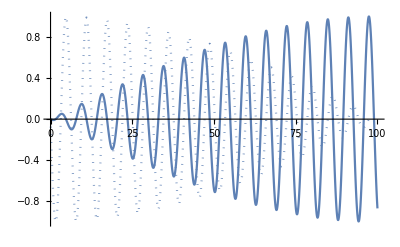

```mathematica
ReImPlot[psi[t,100][[1]],{t,0,100}]
```

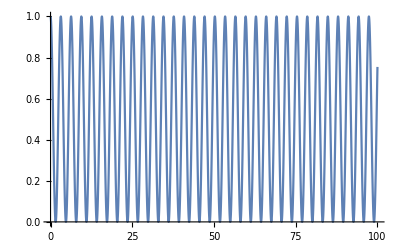

```mathematica
Plot[excitationProbability[t,100],{t,0,100}]
```

## Numerical results

Fidelity is time (t) and final time (Tf) dependent

```mathematica
s=10;
ω[Tf_]:=π/Tf
```

#### Purple basis

```mathematica
Upurple[t_,Tf_]:={{Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ ω[Tf] Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),(2 ⅈ s Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))},{(2 ⅈ s Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),Cos[1/2 t √(4 s^2+ω[Tf]^2)]-(ⅈ ω[Tf] Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))}}
```

```mathematica
groundStatepurple[t_,Tf_]:=eigSortedHfunction[Hpurple[t,Tf]][[1]]
psipurple[t_,Tf_]:=Upurple[t,Tf].groundStatepurple[0,Tf]
fpurple[t_,Tf_]:=Fidelity[groundStatepurple[t,Tf],psipurple[t,Tf]]
```

#### Blue basis

```mathematica
Ublue[t_,Tf_]:={{Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ (ω[Tf] Cos[t ω[Tf]]-2 s Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),(ⅈ (2 s Cos[t ω[Tf]]+ω[Tf] Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))},{(ⅈ (2 s Cos[t ω[Tf]]+ω[Tf] Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ (-ω[Tf] Cos[t ω[Tf]]+2 s Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))}}
```

```mathematica
groundStateblue[t_,Tf_]:=eigSortedHfunction[Hblue[t,Tf]][[1]]
psiblue[t_,Tf_]:=Ublue[t,Tf].groundStateblue[0,Tf]
fblue[t_,Tf_]:=Fidelity[groundStateblue[t,Tf],psiblue[t,Tf]]
```

### Infidelity in time with error - probability of non-excitation

```mathematica
f[t_,Tf_]:=fpurple[t,Tf]
```

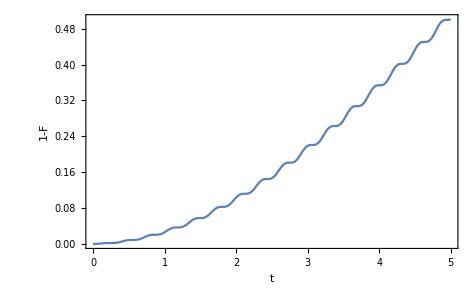

```mathematica
Plot[1-f[t,10],{t,0,5},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"t","1-F"}]
```

### Probability of non-excitation

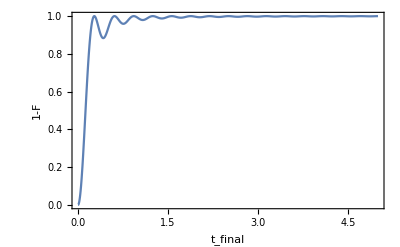

```mathematica
Plot[1-f[Tf,Tf],{Tf,0,5},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

```mathematica
Conjugate[psipurple[t,Tf]].Hpurple[t,Tf].Hpurple[t,Tf].psipurple[t,Tf]
```

```mathematica
N@enVarianceGeod[1,1]
```

3.93738

### Result from the paper - fidelity dependence on Tf

```mathematica
(*Plot[1-f[trev,trev],{trev,0.001,1},PlotRange->All,ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->{"1/t_final","1-F"}]*)
```

### Infidelity dependence on Tf - loglog

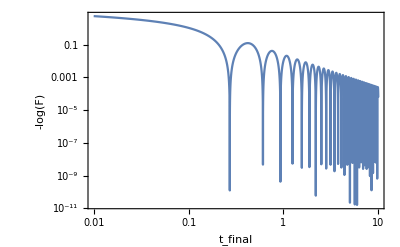

```mathematica
Plot[-Log[1-f[Tf,Tf]],{Tf,0.01,10},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->1000,PerformanceGoal->"Quality",Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}]
```

## Numerical derivation

```mathematica
Clear[s]
Clear[ω]
```

```mathematica
σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
d[t_,s_,Tf_]:={-s Cos[π t/Tf],0,s Sin[π t/Tf]}
```

```mathematica
Hpurple={{Ω,Δ},{Δ,-Ω}}
```

{{Ω,Δ},{Δ,-Ω}}

```mathematica
Hpurple/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}//MatrixForm
```

(-s Cos[t ω] | s Sin[t ω]
s Sin[t ω] | s Cos[t ω])

### Derivation of fidelity

```mathematica
Hblue1=FullSimplify[MatrixExp[-I ω/2 σ[[2]]t].Hpurple.MatrixExp[I ω/2 σ[[2]]t]+ω σ[[2]]/2]
```

{{Ω Cos[t ω]-Δ Sin[t ω],-(ⅈ ω)/2+Δ Cos[t ω]+Ω Sin[t ω]},{(ⅈ ω)/2+Δ Cos[t ω]+Ω Sin[t ω],-Ω Cos[t ω]+Δ Sin[t ω]}}

```mathematica
Hblue=FullSimplify[Hblue1/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}]
```

{{-s,-(ⅈ ω)/2},{(ⅈ ω)/2,s}}

```mathematica
Ublue=FullSimplify[MatrixExp[-I Hblue t],Assumptions->{ω>0,t>0,s>0}]
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),-(ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
Upurple=FullSimplify[MatrixExp[I ω/2 σ[[2]]t].Ublue.MatrixExp[-I ω/2 σ[[2]]t]]
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),-((ω+2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{((ω-2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]-(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
Ψpurplein=Normalize@Eigenvectors[Hpurple/.{Δ->s Sin[0 ω],Ω->-s Cos[0 ω]}][[1]]
```

{1,0}

```mathematica
Ψpurple=FullSimplify[Upurple.Ψpurplein]
```

{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),((ω-2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}

```mathematica
groundStatepurple=FullSimplify[Normalize@Eigenvectors[Hpurple/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}][[1]],Assumptions->{ω>0,t>0,s>0}]
```

{-Cot[(t ω)/2]/(√(1+Abs[Cot[(t ω)/2]]^2)),1/(√(1+Abs[Cot[(t ω)/2]]^2))}

```mathematica
F=FullSimplify[Fidelity[groundStatepurple,Upurple.groundStatepurple],Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

Norm[(Csc[(t ω)/2]^2 (Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))))/(1+Abs[Cot[(t ω)/2]]^2)]^2

```mathematica
Fsimplified=FullSimplify[((8 s^2+ω^2+ω^2 Cos[t √(4 s^2+ω^2)])/(2 (4 s^2+ω^2)))/(Sin[(t ω)/2]^4(1+Abs[Cot[(t ω)/2]]^2)^2)/.ω->π/Tf/.Tf->Subscript[T, f],Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

(Csc[(π t)/(2 T_f)]^4 (π^2 (1+Cos[t √(4 s^2+π^2/T_f^2)])+8 s^2 T_f^2))/(2 (1+Abs[Cot[(π t)/(2 T_f)]]^2)^2 (π^2+4 s^2 T_f^2))

```mathematica
(Csc[(π t)/(2 Subscript[T, f])]^4 (π^2 (1+Cos[t √(4 s^2+π^2/Subscript[T, f]^2)])+8 s^2 Subscript[T, f]^2))/(2 (1+Abs[Cot[(π t)/(2 Subscript[T, f])]]^2)^2 (π^2+4 s^2 Subscript[T, f]^2))
```

#### Finding zero

```mathematica
(Csc[(π t)/(2 Subscript[T, f])]^4 (π^2 (1+Cos[t √(4 s^2+π^2/Subscript[T, f]^2)])+8 s^2 Subscript[T, f]^2))/(2 (1+Abs[Cot[(π t)/(2 Subscript[T, f])]]^2)^2 (π^2+4 s^2 Subscript[T, f]^2))==1
```

```mathematica
Csc[π/2]^4/(2 (1+Abs[Cot[π/2]]^2)^2)
```

1/2

```mathematica
(π^2 (1+Cos[√(T^2+π^2)])+2 T^2)/(2(π^2+T^2))==1
```

```mathematica
1+Cos[√(T^2+π^2)]==(2(π^2+T^2)-2 T^2)/π^2
```

```mathematica
Cos[√(T^2+π^2)]==1
```

Which has solution for k∈Z

```mathematica
√(T^2+π^2)=2k π
```

```mathematica
T=√((2k π)^2-π^2)
```

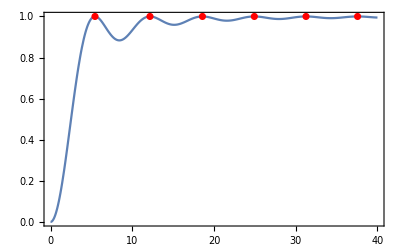

```mathematica
fidelityZeros=Show[Plot[(Csc[π/2]^4 (π^2 (1+Cos[ √(T^2+π^2)])+2 T^2))/(2 (1+Abs[Cot[π/2]]^2)^2 (π^2+T^2)),{T,0,40},Frame->True,PlotRange->All,FrameLabel->MaTeX/@{"T_s","F"}],ListPlot[Table[{√((2k π)^2-π^2),1},{k,1,6}],PlotStyle->Red]]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/fidelityZeros.pdf",fidelityZeros,"AllowRasterization"->True,ImageResolution->800];
```

### In blue coordinate, F = 1 (counterdiabatic driving?)

```mathematica
Ψbluein=Normalize@Eigenvectors[Hblue/.{Δ->s Sin[0 ω],Ω->-s Cos[0 ω]}][[1]]
```

{(ⅈ (2 s+√(4 s^2+ω^2)))/(ω √(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2)),1/(√(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2))}

```mathematica
Ψblue=FullSimplify[Ublue.Ψbluein]
```

{(ⅈ ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(ω √(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2)),(ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)))/(√(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2))}

```mathematica
groundStateblue=FullSimplify[Normalize@Eigenvectors[Hblue/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}][[1]],Assumptions->{ω>0,t>0,s>0}]
```

{(ⅈ (2 s+√(4 s^2+ω^2)))/(ω √(1+((2 s+√(4 s^2+ω^2))^2)/ω^2)),1/(√(1+((2 s+√(4 s^2+ω^2))^2)/ω^2))}

```mathematica
Fblue=FullSimplify[Fidelity[groundStateblue,Ublue.groundStateblue],Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

Norm[(ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(√(ω^2+4 s (2 s+√(4 s^2+ω^2))))]^2

```mathematica
Fbluesimplified=FullSimplify[(ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(√(ω^2+4 s (2 s+√(4 s^2+ω^2))))(ⅇ^(-1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(√(ω^2+4 s (2 s+√(4 s^2+ω^2))))]
```

1

### Energy variance

```mathematica
Ψpurple
```

{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),((ω-2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}

```mathematica
enVarianceGeod=FullSimplify[Conjugate[Ψpurple].Hpurple.Hpurple.Ψpurple-(Conjugate[Ψpurple].Hpurple.Ψpurple)^2/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]},Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

(s^2 (16 s^4+14 s^2 ω^2+ω^4+2 s^2 ((-8 s^2+ω^2) Cos[2 t ω]-8 ω^2 Cos[t ω]^2 Cos[t √(4 s^2+ω^2)])-ω^2 (-2 s^2+(2 s^2+ω^2) Cos[2 t ω]) Cos[2 t √(4 s^2+ω^2)]+8 s^2 ω √(4 s^2+ω^2) Sin[2 t ω] Sin[t √(4 s^2+ω^2)]+ω^3 √(4 s^2+ω^2) Sin[2 t ω] Sin[2 t √(4 s^2+ω^2)]))/(2 (4 s^2+ω^2)^2)

```mathematica
s^2/(2 (4 s^2+ω^2)^2)(16 s^4+14 s^2 ω^2+ω^4+2 s^2 ((-8 s^2+ω^2) Cos[2 t ω]-8 ω^2 Cos[t ω]^2 Cos[t √(4 s^2+ω^2)])-ω^2 (-2 s^2+(2 s^2+ω^2) Cos[2 t ω]) Cos[2 t √(4 s^2+ω^2)]+8 s^2 ω √(4 s^2+ω^2) Sin[2 t ω] Sin[t √(4 s^2+ω^2)]+ω^3 √(4 s^2+ω^2) Sin[2 t ω] Sin[2 t √(4 s^2+ω^2)])
```

## Analytical results

```mathematica
s=10;
ω[Tf_]:=π/Tf
```

```mathematica
(*Fsimplified=(2 (4 s^2+ω^2) (1+Cos[t √(4 s^2+ω^2)])+4 (-2 s Cos[t ω]+ω Sin[t ω])^2 Sin[1/2 t √(4 s^2+ω^2)]^2)/((4 s^2+ω^2) (1+Abs[Sec[t ω]-Tan[t ω]]^2)^2 (1+Sin[t ω])^2);*)
FidelityA[tA_,Tf_]:=Fsimplified/.{Subscript[T, f]->Tf,t->tA}
```

### fidelity in time with error

```mathematica
f[t_,Tf_]:=fpurple[t,Tf]
```

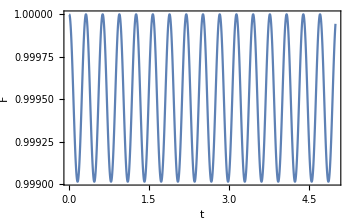

```mathematica
infidelityTimePlot=Plot[FidelityA[t,5],{t,0,5},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"t","F"}]
```

### fidelity on final time - probability of excitation

```mathematica
infidelityTfPlot=Plot[FidelityA[Tf,Tf],{Tf,0,5},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"T_final","F"},PlotLegends->Placed[{"from analytical formula"},{0.75,0.25}]];
```

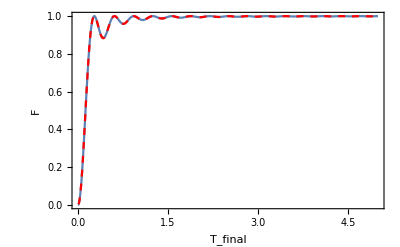

```mathematica
infidelityTfPlotC=Show[{infidelityTfPlot,infidelityTfPlotNumerical}]
```

### Fidelity dependence on Tf - loglog - probability of excitation

```mathematica
infidelityTfPlotLog=Plot[-Log@FidelityA[Tf,Tf],{Tf,0.01,10},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->1000,PerformanceGoal->"Quality",Evaluate@font,Frame->True,FrameLabel->{"T_final","-log(F)"},PlotLegends->Placed[{"from analytical formula"},{0.24,0.3}]];
```

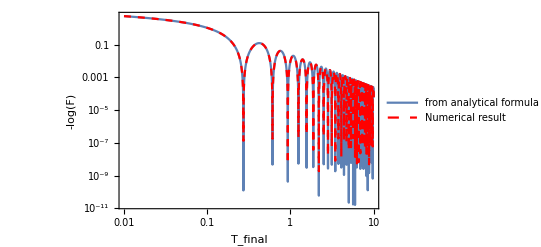

```mathematica
infidelityTfPlotLogC=Show[{infidelityTfPlotLog,infidelityTfPlotLogNumerical}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityTimePlot.pdf",infidelityTimePlot,"AllowRasterization"->True,ImageResolution->800];
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityTfPlot.pdf",infidelityTfPlotC,"AllowRasterization"->True,ImageResolution->800];
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityTfPlotLog.pdf",infidelityTfPlotLogC,"AllowRasterization"->True,ImageResolution->800];
```

### Density plots

```mathematica
dens1=DensityPlot[-Log@FidelityA[t,Tf],{t,0,1},{Tf,0,1},ScalingFunctions->"Log",Evaluate@densityPlotOptionstime,PlotPoints->200,Exclusions->None]
```

-Graphics-

```mathematica
dens3=DensityPlot[-Log@FidelityA[t,Tf],{t,0,10^3},{Tf,0,10^3},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionstime,PlotPoints->200,Exclusions->None]
```

-Graphics-

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/dens1.pdf",dens1,"AllowRasterization"->True,ImageResolution->800];
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/dens3.pdf",dens3,"AllowRasterization"->True,ImageResolution->800];
```

### Energy variance

```mathematica
enVar[t_,Tf_]=FullSimplify[enVarianceGeod/.ω->π/Tf]
```

(50 (π^4+1400 π^2 Tf^2+160000 Tf^4-π^2 Cos[2 t √(400+π^2/Tf^2)] (-200 Tf^2+(π^2+200 Tf^2) Cos[(2 π t)/Tf])+Tf (-1600 π^2 Tf Cos[t √(400+π^2/Tf^2)] Cos[(π t)/Tf]^2+200 Tf (π^2-800 Tf^2) Cos[(2 π t)/Tf]+2 π √(400+π^2/Tf^2) (400 Tf^2+π^2 Cos[t √(400+π^2/Tf^2)]) Sin[t √(400+π^2/Tf^2)] Sin[(2 π t)/Tf])))/((π^2+400 Tf^2)^2)

```mathematica
densVar=DensityPlot[enVar[t,Tf],{t,1,100},{Tf,1,100},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionstime,PlotPoints->600,Exclusions->None]
```

-Graphics-

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/densVar.pdf",densVar,"AllowRasterization"->True,ImageResolution->800];
```

# Linear driving

## inFidelityLinNonC[t,Tf,Ωconst] inFidelityLin[t,Tf,Ωconst] Hl[t, Tf, Ωconst] psi[t, Tf, Ωconst] enVariance[t, Tf, Ωconst]

```mathematica
inFidelityLinNonC[t_,Tf_,Ωconst_]:=Module[{Ω,Δ,sqr,qq,gam,Δfi,Δi,u,T,ui,en,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ω[T_]:=Ωconst;
Δ[T_]:=Δl[T/Tf];
sqr=√(Tf^-1 Δfi);
om=Ω[0]/sqr;

Δfi=Δ[Tf]-Δ[0];
Δi=Δ[0];

u[T_]:=Δ[T]/sqr;
ui=u[0];
en[T_]:=Eigenvalues[H[Δ[T],Ω[T]]][[1]];
ent[T_]:=en[T]/sqr;

enti=ent[0];

(*Q0 and Q1 at initial time*)
qq=1/2 1/(√(enti(enti-om)));
Q00=qq(om-ui-enti);

Q10=qq(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0[T_]:=a0t ParabolicCylinderD[n,(1-I)u[T]]+b0t ParabolicCylinderD[n,(I-1)u[T]];
Q1[T_]:=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u[T]]-b0t ParabolicCylinderD[n-1,(I-1)u[T]]);
(*Real part needs to be added due to numerical error*)
Re[1/2(1+u[t]/ent[t])-u[t]/ent[t](Conjugate[Q0[t]]Q0[t]-om/u[t] Re[Conjugate[Q0[t]]Q1[t]])]

]
inFidelityLin=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{sqr,qc,gam,Ω,Δ,Δfi,Δi,u,T,ui,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ωscale=10;
Δ=Ωscale (-1+2 t/Tf);

Δfi=2Ωscale;
sqr=√(Tf^-1 Δfi);
om=Ωconst/sqr;
Δi=-Ωscale;

u=Δ/sqr;
ui=Δi/sqr;
ent=(-√(Δ^2+Ωconst^2))/sqr;
enti=-(√(Ωscale^2+Ωconst^2))/sqr;

(*Q0 and Q1 at initial time*)
qc=1/2 1/(√(enti(enti-om)));
Q00=qc(om-ui-enti);
Q10=qc(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0=a0t ParabolicCylinderD[n,(1-I)u]+b0t ParabolicCylinderD[n,(I-1)u];
Q1=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u]-b0t ParabolicCylinderD[n-1,(I-1)u]);
(*Real part needs to be added due to numerical error*)
1/2(1+u/ent)-u/ent(Conjugate[Q0]Q0-om/u Re[Conjugate[Q0]Q1])

],CompilationTarget->"C",RuntimeOptions->"EvaluateSymbolically"->False]
Hl=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{Ω,Δ},
Ω=Ωconst;
Δ=Ωscale (-1+2 t/Tf);
{{Ω,Δ},{Δ,-Ω}}
],CompilationTarget->"C",RuntimeOptions->"EvaluateSymbolically"->False]
psi=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{sqr,qc,gam,Ω,Δ,Δfi,Δi,u,T,ui,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ωscale=10;
Δ=Ωscale (-1+2 t/Tf);

Δfi=2Ωscale;
sqr=√(Tf^-1 Δfi);
om=Ωconst/sqr;
Δi=-Ωscale;

u=Δ/sqr;
ui=Δi/sqr;
ent=(-√(Δ^2+Ωconst^2))/sqr;
enti=-(√(Ωscale^2+Ωconst^2))/sqr;

(*Q0 and Q1 at initial time*)
qc=1/2 1/(√(enti(enti-om)));
Q00=qc(om-ui-enti);
Q10=qc(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0=a0t ParabolicCylinderD[n,(1-I)u]+b0t ParabolicCylinderD[n,(I-1)u];
Q1=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u]-b0t ParabolicCylinderD[n-1,(I-1)u]);
1/(√2){Q1+Q0,Q1-Q0}

],CompilationTarget->"C",RuntimeOptions->"EvaluateSymbolically"->False]
enVariance[t_,Tf_,Ωconst_]:=Module[{p,h},
p=psi[t,Tf,Ωconst];
h=Hl[t,Tf,Ωconst];
Re[Conjugate[p].h.h.p-(Conjugate[p].h.p)^2]
]
```

CompiledFunction[…]

CompiledFunction[…]

CompiledFunction[…]

## Density plots

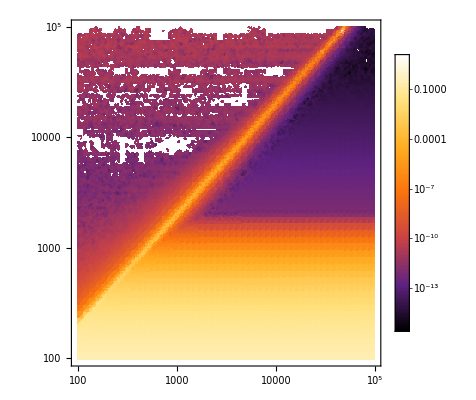

```mathematica
dens1=DensityPlot[-Log[1-inFidelityLin[t,Tf,0.3]],{t,0,10^5},{Tf,0,10^5},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"t","T_f"},PlotPoints->50,Exclusions->None]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/dens1Lin.pdf",dens1,"AllowRasterization"->True,ImageResolution->800];
```

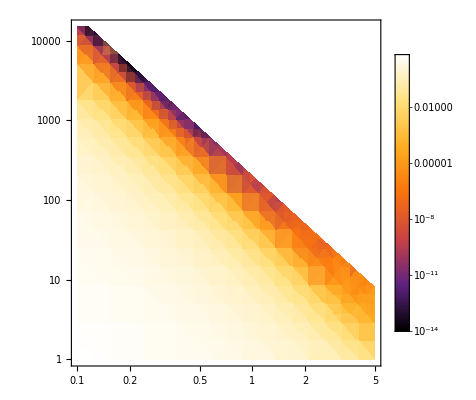

```mathematica
dens2Unzoom=DensityPlot[
Piecewise[{{-Log[1-inFidelityLin[Tf,Tf,Ωconst]],200/Ωconst^2>Tf}},0]
,{Ωconst,0.1,5},{Tf,1,15000},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->10,Exclusions->None]
```

```mathematica
dens2=DensityPlot[-Log[1-inFidelityLin[Tf,Tf,Ωconst]],{Ωconst,0.5,4},{Tf,1,500},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->50,Exclusions->None]
```

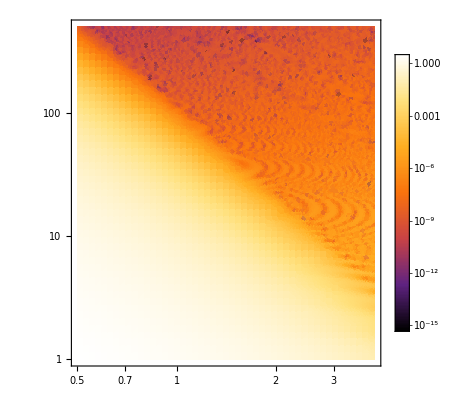

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/dens2.pdf",dens2,"AllowRasterization"->True,ImageResolution->800];
```

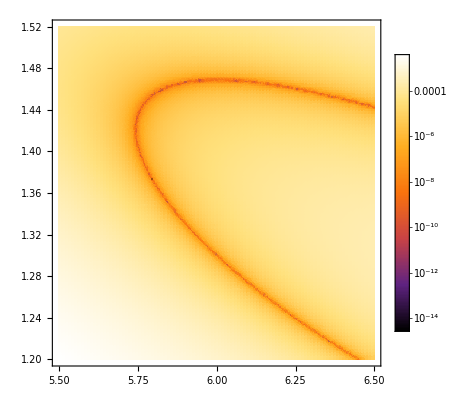

```mathematica
dens2Zoom=DensityPlot[-Log[1-inFidelityLin[Tf,Tf,Ωconst]],{Ωconst,5.5,6.5},{Tf,1.2,1.52},ScalingFunctions->"Log",Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->100,Exclusions->None]
```

```mathematica
densVariance=DensityPlot[enVariance[t,Tf,0.2],{t,0,100},{Tf,1,100},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionstime,PlotPoints->100,Exclusions->None]
```

-Graphics-

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/densVariance.pdf",densVariance,"AllowRasterization"->True,ImageResolution->800];
```

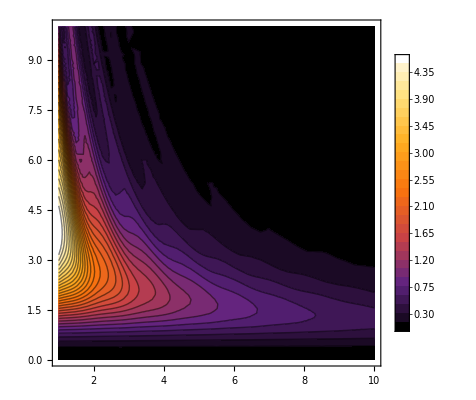

```mathematica
contVariance=ContourPlot[enVariance[Tf/2,Tf,Ω],{Tf,1,10},{Ω,0.01,10},PlotPoints->10,Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"T_f","\\Omega"},Contours->30]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/contVariance.pdf",contVariance,"AllowRasterization"->True,ImageResolution->800];
```

## Fidelity time and final time dependence

### Infidelity in time with error

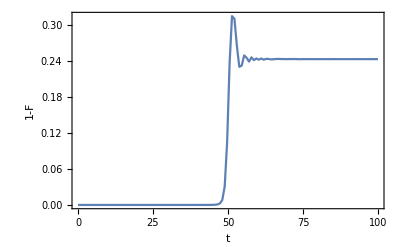
{0.861322,-Graphics-}

```mathematica
infidelityTimePlot=Timing@Plot[inFidelityLin[t,100,0.3],{t,0,100},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"t","1-F"},PlotPoints->3]
```

### Infidelity on final time - probability of non-excitation

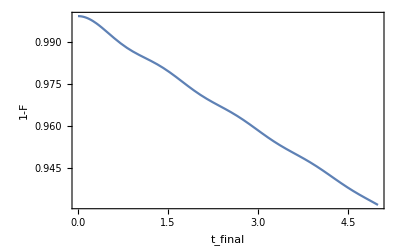

```mathematica
infidelityTfPlot=Plot[inFidelityLin[Tf,Tf,0.3],{Tf,0,5},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"}]
```

### Fidelity dependence on Tf - loglog - probability of excitation

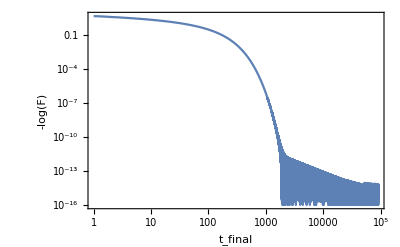

```mathematica
infidelityTfPlotLog=Plot[-Log[1-inFidelityLin[Tf,Tf,0.3]],{Tf,1,10^5},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->1000,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityTimePlotLin.pdf",infidelityTimePlot,"AllowRasterization"->True,ImageResolution->800];
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityTfPlotLin.pdf",infidelityTfPlot,"AllowRasterization"->True,ImageResolution->800];
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityTfPlotLogLin.pdf",infidelityTfPlotLog,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
fidZOOM=Plot[-Log[1-inFidelityLin[Tf,Tf,0.3]],{Tf,1883,1893},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->100,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"},AspectRatio->1/5,ImageSize->1500]
```

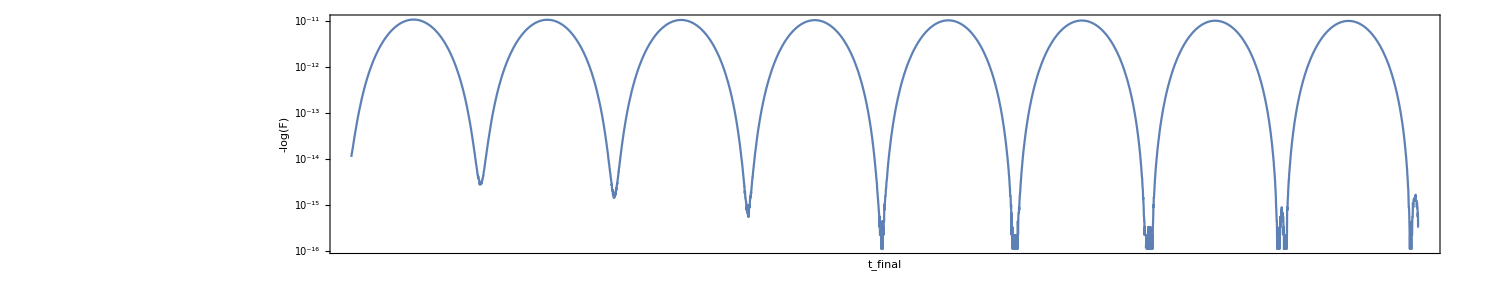

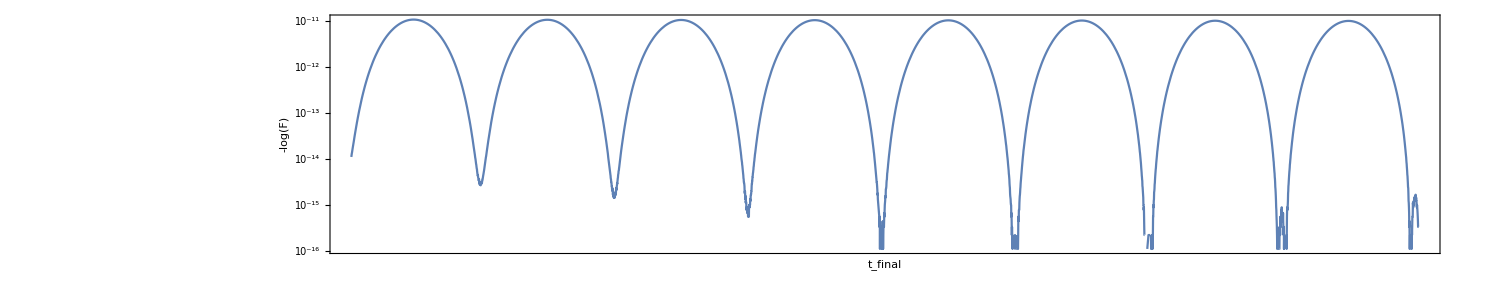

```mathematica
fidZOOM=Plot[fidelityLogNonC[Tf,Tf,0.3],{Tf,1883,1893},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->100,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"},AspectRatio->1/5,ImageSize->1500]
```

```mathematica
fidZOOMroots=Quiet@FindRoot[fidelityLogNonC[Tf,Tf,0.3],{Tf,#},AccuracyGoal->Infinity,PrecisionGoal->100,WorkingPrecision->100]&/@Range[1883,1890,1]
```

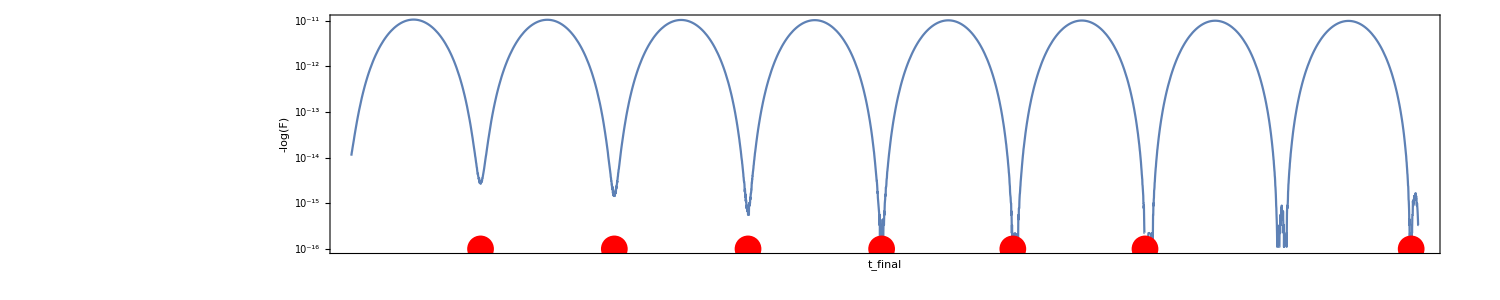

```mathematica
Show[{
fidZOOM,
ListPlot[Transpose@{Tf/.fidZOOMroots,ConstantArray[10^-16,Dimensions[fidZOOMroots][[1]]]},ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"},PlotStyle->Red]
}]
```

```mathematica
periodeTab={{0.3,(1893-1883)/8},{0.6,(1893-1883)/16},{1.2,(1893-1883)/17},{3,(1893-1883)/20}} ;
```

#### => perioda=f(Ω,Tf)

### Minimas are in zero :

```mathematica
infidelityTfPlotLogZoom=Plot[-Log[1-inFidelityLin[Tf,Tf,0.3]],{Tf,1000,4000},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->100,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}];
```

```mathematica
finalFidelityMinimasLin=Quiet@FindRoot[-Log[1-inFidelityLinNonC[Tf,Tf,0.3]],{Tf,#},WorkingPrecision->100]&/@Range[1500,3000,10];
```

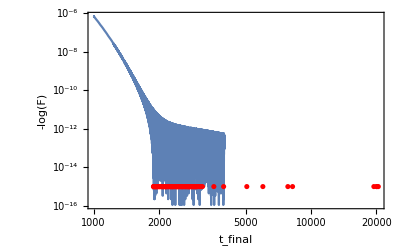

```mathematica
Show[{
infidelityTfPlotLogZoom,
ListPlot[Transpose@{Tf/.finalFidelityMinimasLin,ConstantArray[10^-15,Dimensions[finalFidelityMinimasLin][[1]]]},ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"},PlotStyle->Red]
}]
```

```mathematica
Table[Tf/.Min@FindRoot[-Log[1-inFidelityLinNonC[Tf,Tf,0.5]],{Tf,tff},WorkingPrecision->100],{tff,100,2000,400}]
```

FindRoot::precw: The precision of the argument function (-Log[0.999376-0.998752 (-0.05 Re[Times[«4»]]+Re[Conjugate[«1»] Plus[«2»]])]) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1704.369295232520059831995790626059216785463892718679146474186486343743438717576050126220383585343626,637.4443257489672129941418722047940214096643450720577874437736510555823703933935588217559661279965931,899.7514689308153613619789434978322082006689840080199130318717643205550962186187968264434031628808922,1300.194790948595426486324030454377393273607173373016037133474207115343231486171447475068428618314307,1700.016647914308055251323845875878842797793082118491222669309769849358432046095092935666112020970787}

```mathematica
TcFromRootTab=ParallelTable[{Ω,Min[Table[Tf/.Quiet@FindRoot[-Log[1-inFidelityLinNonC[Tf,Tf,Ω]],{Tf,tff},WorkingPrecision->70],{tff,500,5000,200}]]},{Ω,0.3,1.5,0.1}];
```

```mathematica
(*TcFromRootTab=DeleteCases[TcFromRootTab,{om_,root_}/;root<0]*)
```

```mathematica
TcFromRootTab=TcFromRootTab[[2;;-1]];
```

-256.506/om^2+776.296/om

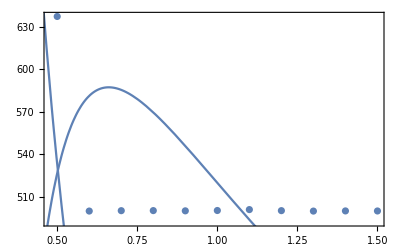

```mathematica
TcFromRootFit=Fit[TcFromRootTab,{om^-1,om^-2},om]
Show[{ListPlot[TcFromRootTab,Frame->True,PlotRange->All,FrameLabel->MaTeX/@{"\\Omega","T_c"}],Plot[TcFromRootFit,{om,0.1,3.0},PlotRange->All],
Plot[1.2 121.06976126016289/om^2-0.46 52.422291233262946/om,{om,0.1,3.0},PlotRange->All]}]
```

```mathematica
}
```

One can see that this dependence copies the boundary between singular and smooth behaviour in DensityPlot pretty nicely

```mathematica
Manipulate[Show[{dens2,ContourPlot[Tf==a 121/om^2+b 52/om,{om,0.1,5},{Tf,1,15000},PlotRange->All,ScalingFunctions->{"Log","Log","Log"}]}],{{a,1.2},0.1,10},{{b,-0.46},-5,5}]
```

## Checking the Tc=Tc(Ω) dependence manually

### Plots

```mathematica
critTimeOnEnPlots=ParallelMap[Plot[-Log[1-inFidelityLin[Tf,Tf,#]],{Tf,1,10^4},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->3,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}]&,Range[0.1,2,0.1]]
```

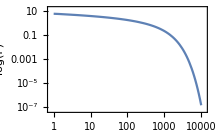
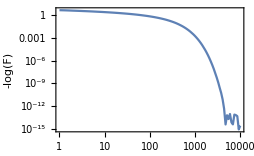
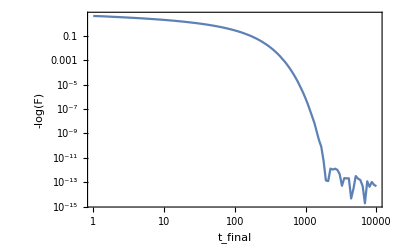
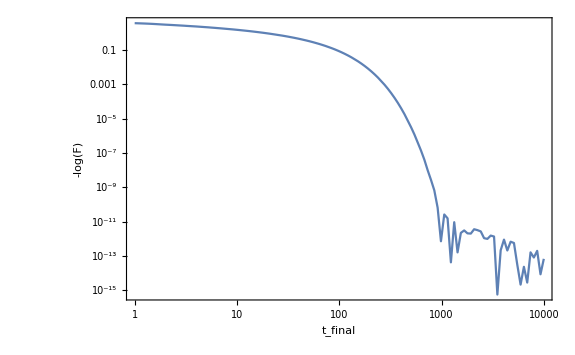
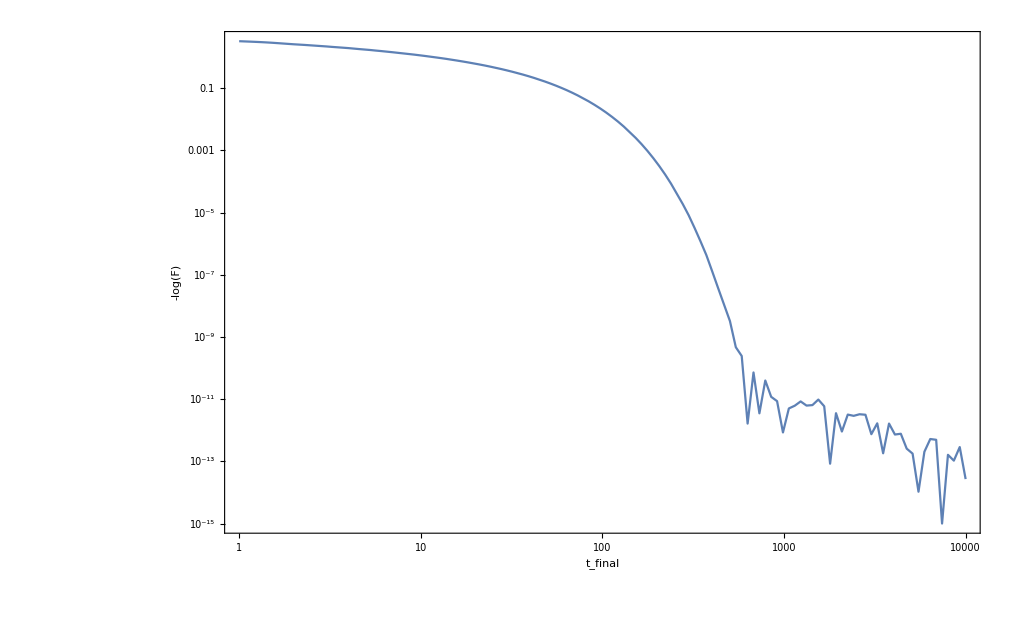
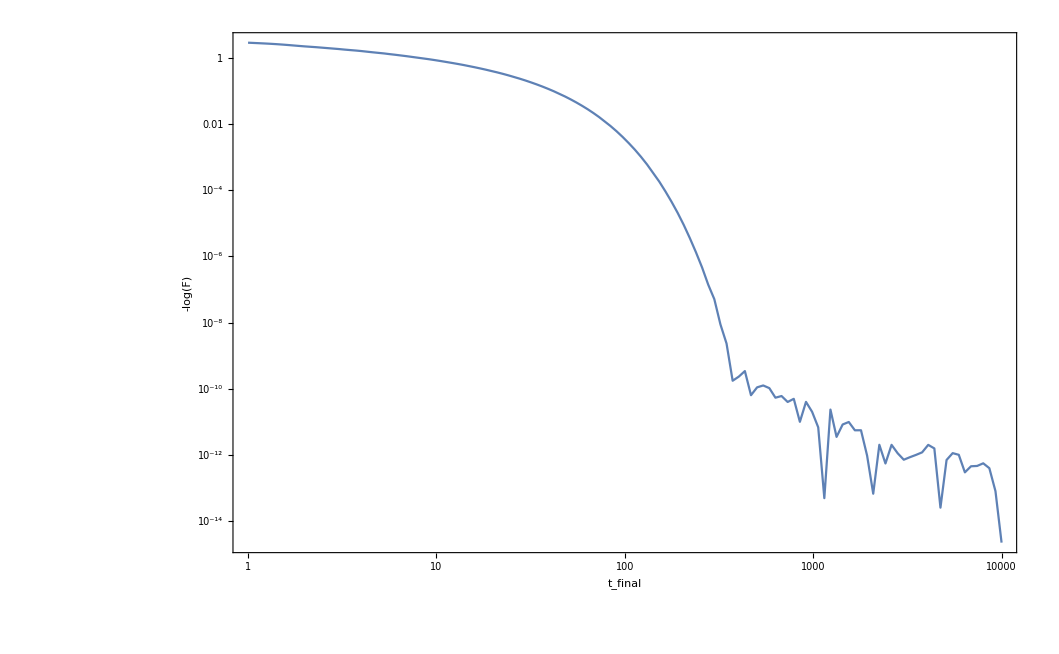
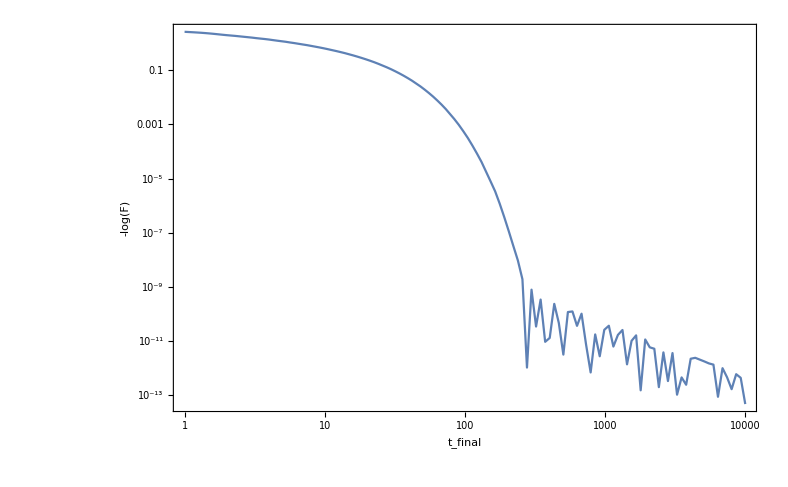
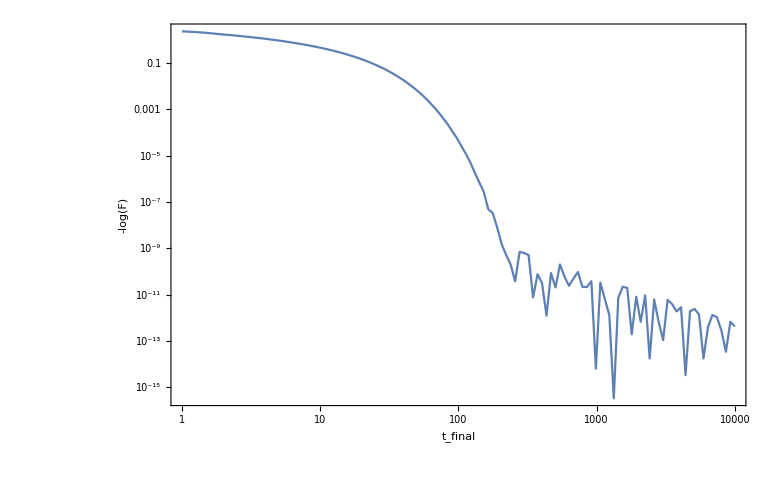

### From plots - Tc=Tc(Ωconst)

From plots above, the coordinates (Ω_crit;T_crit) was written out

```mathematica
TcOmega={{0.2,4700},{0.3,2100},{0.4,1000},{0.5,650},{0.6,390},{0.7,280},{0.8,260},{0.9,175},{1.0,142},{1.1,95},{1.2,71},{1.3,61},{1.4,50},{1.5,40},{1.6,39},{1.7,31},{1.8,29},{1.9,23},{2.0,22}};
```

185.158/om^2

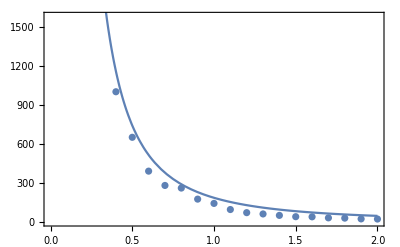

```mathematica
TcOmegaFit=Fit[TcOmega,{om^-2},om]
Show[{ListPlot[TcOmega,Frame->True,FrameLabel->MaTeX/@{"\\Omega","T_c"}],Plot[TcOmegaFit,{om,0.2,2.0}]}]
```

## Tc=Tc(ΔE_01)

### From Hamiltonian - energy difference ΔE_01 on Ωconst

```mathematica
ΔE01[Ω_]:=2 √(0^2+Ω^2)
```

```mathematica
TcOnΔE01=FullSimplify[TcFromRootFit/.om->ΔE01/2]
```

```mathematica
Plot[TcOnΔE01,{ΔE01,0.1,3},Frame->True,PlotRange->All,FrameLabel->MaTeX/@{"\\Delta E_{01}","T_c"}]
```

## δE^2=δE^2(Ωconst(ΔE_01))

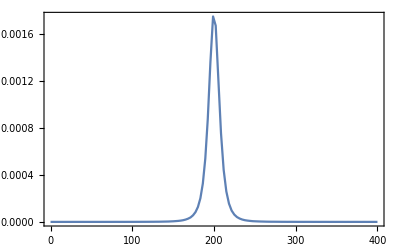
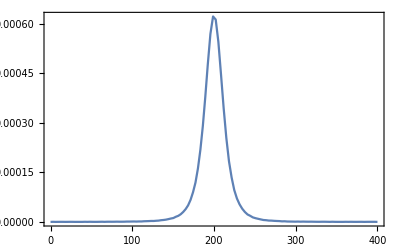
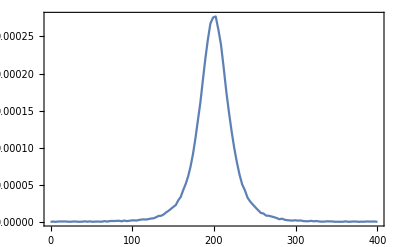

```mathematica
Plot[enVariance[t,400,#],{t,0,400},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","\\delta E^2"},PlotRange->All,PlotPoints->3]&/@{0.6,1,1.5}
```

### δE^2=δE^2(Ω) for T_c=T_f and t=T_c/2

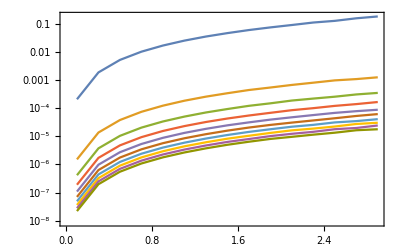

```mathematica
ListLinePlot[Table[ParallelTable[{Ω,enVariance[a Tc[Ω]/2,a Tc[Ω],Ω]},{Ω,0.1,3,0.2}],{a,0.1,10,1}],ScalingFunctions->"Log",Frame->True,FrameLabel->MaTeX/@{"\\Omega","\\delta E^2"}]
```

```mathematica
Plot[enVariance[Tc/2,Tc,2],{Tc,0.1,10}]
```

$Aborted

{{0.1,3.14868×10^-6},{0.2,0.0000125948},{0.3,0.0000283367},{0.4,0.0000503735},{0.5,0.0000786993},{0.6,0.000113368},{0.7,0.000154283},{0.8,0.000201315},{0.9,0.000255072},{1.,0.000315486},{1.1,0.000380638},{1.2,0.000454841},{1.3,0.00053024},{1.4,0.000615732},{1.5,0.000711342},{1.6,0.000800626},{1.7,0.000916053},{1.8,0.00102962},{1.9,0.00112845},{2.,0.00125305},{2.1,0.0013754},{2.2,0.00149872},{2.3,0.00164915},{2.4,0.00182478},{2.5,0.00201793},{2.6,0.00209577},{2.7,0.00225335},{2.8,0.00253062},{2.9,0.0027008},{3.,0.00289496}}

0.000316847 Ω^2

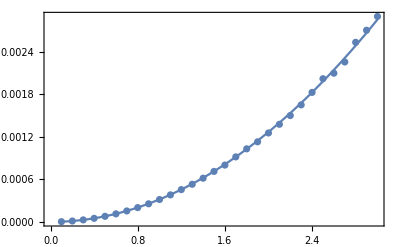

```mathematica
enVarianceTcTab=ParallelTable[{Ω,enVariance[(4a)/(2 Ω^2),(4a)/Ω^2,Ω]},{Ω,0.1,3,0.1}]
enVarianceTcFit=Fit[enVarianceTcTab,{Ω^2},Ω]
Show[{
ListPlot[enVarianceTcTab,Frame->True,FrameLabel->MaTeX/@{"\\Omega","\\delta E^2"}],
Plot[enVarianceTcFit,{Ω,0.1,3}]
}]
```

### Max δE^2=δE^2|_(t=Tc/2)=δE^2(t=Tc/2,T_f,Ω)

```mathematica
maxVarianceTfTab=ParallelTable[{Tf,enVariance[Tf/2,Tf,2]},{Tf,60,5000,50}];
```

116.833/Tf^2

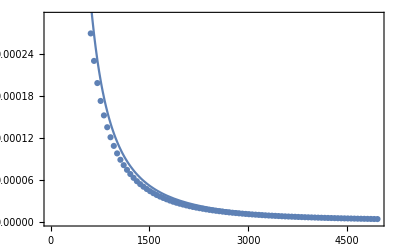

```mathematica
maxVarianceTfFit=Fit[maxVarianceTfTab,{Tf^-2},Tf]
Show[{
ListPlot[maxVarianceTfTab,Frame->True,FrameLabel->MaTeX/@{"T_f","\\delta E^2\\big|_{t=T_f/2}"}],
Plot[maxVarianceTfFit,{Tf,60,5000}]
}]
```

114.94/omega^2

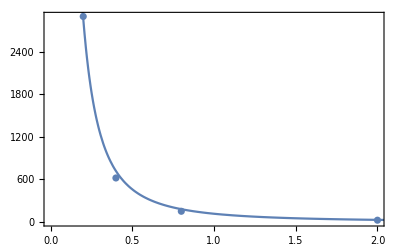

```mathematica
konstOmegaTab={{0.2,2900},{0.4,620},{0.8,150},{2,24}};
konstOmegaFit=Fit[konstOmegaTab,{omega^-2},omega]
Show[{ListPlot[konstOmegaTab,Frame->True,FrameLabel->MaTeX/@{"\\Omega","konst"}],
Plot[konstOmegaFit,{omega,0.02,3},PlotRange->All]}]
```

Fit does not converge sometimes, but putting it all together, we get approximation for konst=115/Ω^2 for Ω∈[0.2,3]

```mathematica
Ωtest=0.2;
maxVarianceTfTab=ParallelTable[{Tf,enVariance[Tf/2,Tf,Ωtest]},{Tf,60,5000,50}];
Manipulate[Show[{
ListPlot[maxVarianceTfTab,Frame->True,FrameLabel->MaTeX/@{"T_f","\\Delta E^2\\big|_{t=T_f/2}"}],
Plot[a/Tf^2,{Tf,60,5000},PlotStyle->Red]
}],{{a,110/Ωtest^2},10,3000}]
```

SetPrecision::precsm: Requested precision 5 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

ListPlot::lpn: maxVarianceTfTab is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[maxVarianceTfTab,Frame→True,FrameLabel→{,}],}].

Therefore ΔE_01(T_f)=110/(Ω^2 T_f^2)for Ω∈[0.2,3]

### Some plots for fun

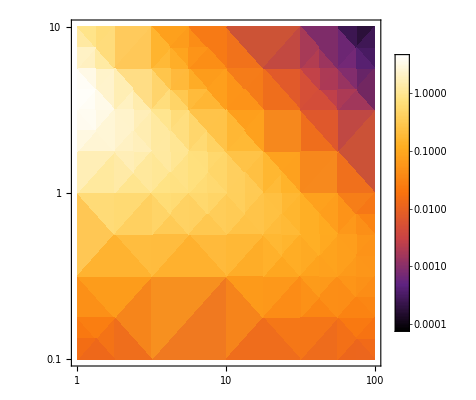

```mathematica
dens3=DensityPlot[enVariance[Tf/2,Tf,const],{Tf,1,10^2},{const,0.1,10},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsParam,PlotPoints->5,Exclusions->None]
```

```mathematica
(*densVarianceTab=Flatten[ParallelTable[{t,Tf,enVariance[t,Tf,0.2]},{t,1,1000,10},{Tf,1,10,2}],1];
ListDensityPlot[densVarianceTab,ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsParam]*)
```

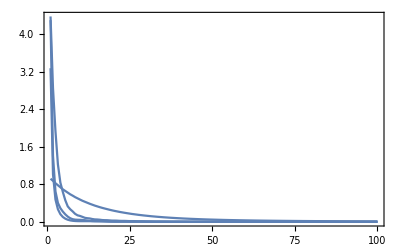

```mathematica
Plot[enVariance[Tf/2,Tf,#]&/@{1,3,5,7},{Tf,1,100},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","\\Delta E^2"},PlotRange->All,PlotPoints->3]
```

```mathematica
enVariance[10^3/2,10^3,1]
```

0.000100207

```mathematica
tab1=Flatten[ParallelTable[{Tf,omega,enVariance[Tf/2,Tf,omega]},{Tf,1,10^4,1000},{omega,0.1,2,0.1}],1]
```

$Aborted

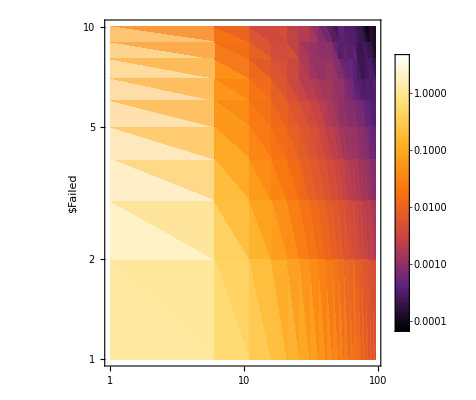

```mathematica
ListDensityPlot[tab1,ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsParam]
```

## Putting it all together

We have formulas
ΔE_01=2Ω for Δ=0
T_c=a/ΔE_01^2for a≈141 (good approximation for transition between chaotic and smooth areas)
δE^2=b Ω^2 for b≈0.000316847 (holds for Ω∈[0.2,3], might be exact and I don’t see it due to numerical errors, or the same chaotic principles as above are applied)

```mathematica
a=141;
b=0.000316847;
```

From these goes T_c=a/ΔE_01^2=a/(4 Ω^2)=(a b)/(4 δE^2)

```mathematica
TcOnδE2=(141 0.000185)/(4δE2)
```

0.00652125/δE2

Recalculated to the speed in parametric space: on the line we have distance s_parametric=√((Ω_f-Ω_i)^2+(Δ_f-Δ_i)^2)=20

```mathematica
parametricSpeed=20/TcOnδE2
```

3066.9 δE2

Generally comparable quantity is not T_c, but geodesical distance s=∫√(g_μν Λ^μ Λ^ν)

```mathematica
geodDistance[Ωg_]:=Module[{Ωscale,Ωlg,Δlg,t},
Ωscale=10;
Ωlg[t_]:=Ωg;
Δlg[t_]:=Ωscale (-1+2 t);
L=√({Δlg'[t],Ωlg'[t]}.g[Δlg[t],Ωlg[t]].{Δlg'[t],Ωlg'[t]});
NIntegrate[L,{t,0,(4a)/Ωg}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$142825 near {t$142825} = {0.55896}. NIntegrate obtained 17.7147 and 0.58743 for the integral and error estimates.

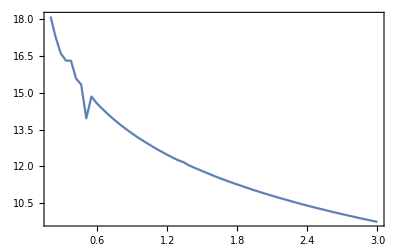

```mathematica
Plot[geodDistance[Ω],{Ω,0.2,3},PlotPoints->2,Frame->True,Evaluate@font,FrameLabel->MaTeX/@{"\\Omega","s"}]
```

Therefore critical geodesical speed v_c=s/T_c

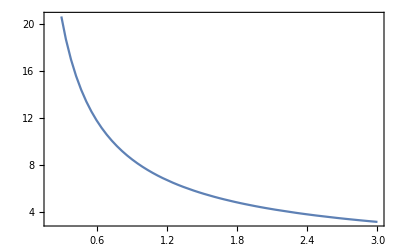

```mathematica
Plot[geodDistance[1/2 √(a/Tc)]/Tc,{Tc,0.2,3},PlotPoints->2,Frame->True,Evaluate@font,FrameLabel->MaTeX/@{"T_c","v_c"}]
```

## Localizing elements from Fidelity formula

```mathematica
inFidelityLinp4=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{sqr,qc,gam,Ω,Δ,Δfi,Δi,u,T,ui,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ωscale=10;
Δ=Ωscale (-1+2 t/Tf);

Δfi=2Ωscale;
sqr=√(Tf^-1 Δfi);
om=Ωconst/sqr;
Δi=-Ωscale;

u=Δ/sqr;
ui=Δi/sqr;
ent=(-√(Δ^2+Ωconst^2))/sqr;
enti=-(√(Ωscale^2+Ωconst^2))/sqr;

(*Q0 and Q1 at initial time*)
qc=1/2 1/(√(enti(enti-om)));
Q00=qc(om-ui-enti);
Q10=qc(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0=a0t ParabolicCylinderD[n,(1-I)u]+b0t ParabolicCylinderD[n,(I-1)u];
Q1=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u]-b0t ParabolicCylinderD[n-1,(I-1)u]);
(*Real part needs to be added due to numerical error*)
Re[Conjugate[Q0]Q1]

],CompilationTarget->"C",RuntimeOptions->"EvaluateSymbolically"->False];
```

### 1/2(1+u/ent)

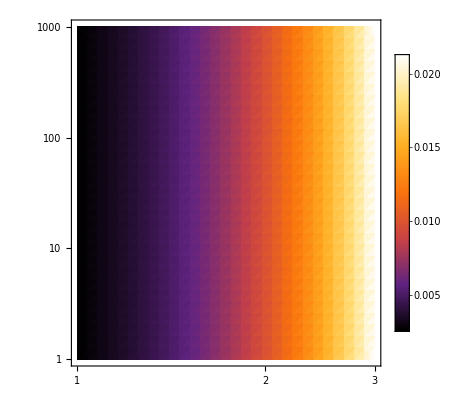

```mathematica
DensityPlot[
-Log[1-inFidelityLinp7[Tf,Tf,Ωconst]]
,{Ωconst,1,3},{Tf,1,1000},ScalingFunctions->{"Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->30,Exclusions->None]
```

### ω/u

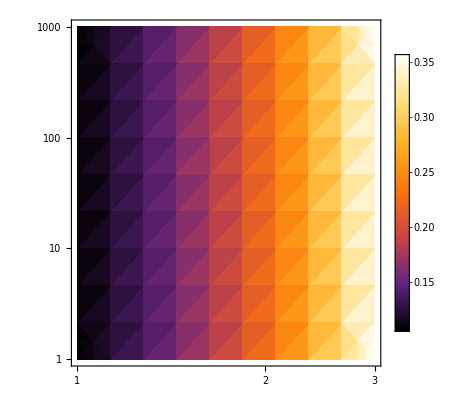

```mathematica
DensityPlot[
-Log[1-inFidelityLinp5[Tf,Tf,Ωconst]]
,{Ωconst,1,3},{Tf,1,1000},ScalingFunctions->{"Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->10,Exclusions->None]
```

### Re[Conjugate[Q0] Q1]

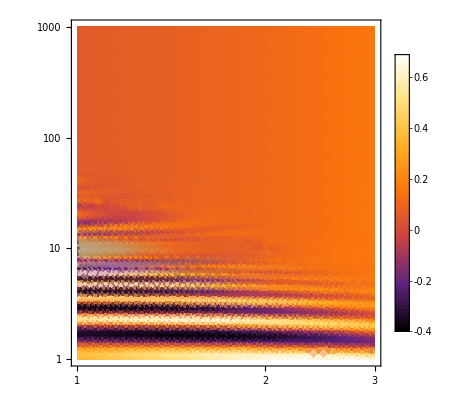

```mathematica
DensityPlot[
-Log[1-inFidelityLinp4[Tf,Tf,Ωconst]]
,{Ωconst,1,3},{Tf,1,1000},ScalingFunctions->{"Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->30,Exclusions->None]
```

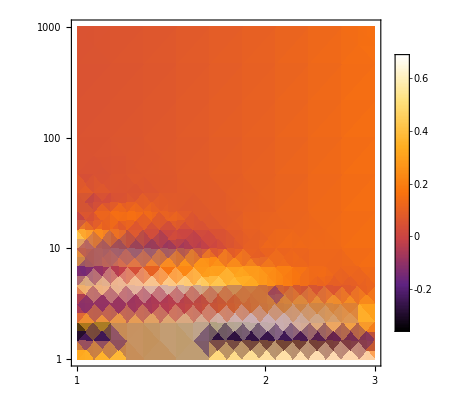

```mathematica
DensityPlot[
-Log[1-inFidelityLinp4[Tf,Tf,Ωconst]]
,{Ωconst,1,3},{Tf,1,1000},ScalingFunctions->{"Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->10,Exclusions->None]
```

### Q0^2

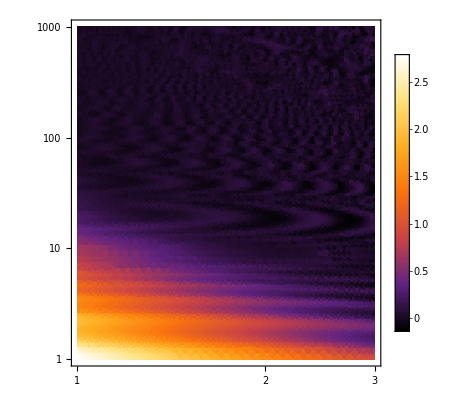

```mathematica
DensityPlot[
-Log[1-inFidelityLinp6[Tf,Tf,Ωconst]]
,{Ωconst,1,3},{Tf,1,1000},ScalingFunctions->{"Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->30,Exclusions->None]
```

### Re[Q1]

```mathematica
DensityPlot[
-Log[1-inFidelityLinp7[Tf,Tf,Ωconst]]
,{Ωconst,1,3},{Tf,1,1000},ScalingFunctions->{"Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->30,Exclusions->None]
```

-Graphics-

### Re[Q0]

```mathematica
DensityPlot[
-Log[1-inFidelityLinp6[Tf,Tf,Ωconst]]
,{Ωconst,1,3},{Tf,1,1000},ScalingFunctions->{"Log","Log"},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Omega","T_f"},PlotPoints->30,Exclusions->None]
```

-Graphics-

## Fidelity slope

```mathematica
Plot[-Log[1-inFidelityLin[Tf,Tf,0.3]],{Tf,10^4,10^6},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->3,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}]
```

-Graphics-

```mathematica
Table[{k,Max[Table[Tf,{Tf,k,20+k}]]},{k,1,100,10}]
```

{{1,21},{11,31},{21,41},{31,51},{41,61},{51,71},{61,81},{71,91},{81,101},{91,111}}

```mathematica
smoothFidelity[Ω_,Ωmin_,Ωmax_,averageOverN_,qualityP_]:=Quiet@Table[{k,
Max@ParallelTable[-Log[1-inFidelityLin[Tf,Tf,Ω]],{Tf,k,averageOverN+k,qualityP}]},{k,200/Ω^2,Ωmax,averageOverN}]
```

```mathematica
ListLinePlot[{
smoothFidelity[0.2,50/Ω^2,3 10^4,500,100],smoothFidelity[0.3,50/Ω^2,3 10^4,500,100],smoothFidelity[0.4,50/Ω^2,3 10^4,500,100],smoothFidelity[0.5,50/Ω^2,3 10^4,500,100],smoothFidelity[0.6,50/Ω^2,3 10^4,500,100]
},ScalingFunctions->{"Log","Log"}]
```

-Graphics-

```mathematica
ListLinePlot[
Table[ParallelTable[-Log[1-inFidelityLin[Tf,Tf,om]],{Tf,1,10^4,1000}]%,{om,1.5,5,1}],
ScalingFunctions->{"Log","Log"}]
```

CompiledFunction::cfse: Compiled expression 2.52496403627902×10^317-9.32045407931733×10^316 ⅈ should be a machine-size complex number.

CompiledFunction::cfse: Compiled expression 2.73747985420418×10^369+4.91818857592325×10^370 ⅈ should be a machine-size complex number.

CompiledFunction::cfse: Compiled expression -3.91426682902638×10^423+8.22430395469054×10^423 ⅈ should be a machine-size complex number.

CompiledFunction::cfse: Compiled expression 1.63978215632252×10^477-4.38952197447452×10^476 ⅈ should be a machine-size complex number.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

General::munfl: Exp[-738.59+2413.79 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression (-0.926823+0.355065 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.980995+0.150731 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.990665-0.0604414 ⅈ)/(0.+0. ⅈ) encountered.

General::munfl: Exp[-738.59-2413.79 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-861.385+2900.45 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-984.17+3398.31 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1106.95+3905.96 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-738.59-2413.79 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression (-0.5208565863438219+0.8271326441306626 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.9592618969240798-0.187767430154271 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.17055711807681-0.9624709160932927 ⅈ)/(0.+0. ⅈ) encountered.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.926823+0.355065 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.980995+0.150731 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.990665-0.0604414 ⅈ)/(0.+0. ⅈ) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::munfl: Exp[-861.385-2900.45 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-984.17-3398.31 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1106.95-3905.96 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-861.385-2900.45 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-984.17-3398.31 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1106.95-3905.96 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression -9.143263579283×10^310+1.41771447736627×10^311 ⅈ should be a machine-size complex number.

CompiledFunction::cfse: Compiled expression 2.79657395755028×10^414+4.20499351617669×10^415 ⅈ should be a machine-size complex number.

CompiledFunction::cfse: Compiled expression -2.95998217245382×10^519+1.04622076345737×10^520 ⅈ should be a machine-size complex number.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression -8.06255963177531×10^622+2.86191657664794×10^624 ⅈ should be a machine-size complex number.

General::munfl: Exp[-723.971+2356.69 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression (0.267418+0.948903 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.263271-0.950062 ⅈ)/(0.+0. ⅈ) encountered.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

General::munfl: Exp[-723.971-2356.69 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-964.643+3318.45 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1205.28+4318.89 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression (0.259132+0.951229 ⅈ)/(0.+0. ⅈ) encountered.

General::munfl: Exp[-723.971-2356.69 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression (0.7712757728249704-0.5672141873113072 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.6826160022993475-0.6712927906020149 ⅈ)/(0.+0. ⅈ) encountered.

General::munfl: Exp[-1445.9+5350.15 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.5542358021066209+0.7806620747909063 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (0.267418+0.948903 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.263271-0.950062 ⅈ)/(0.+0. ⅈ) encountered.

CompiledFunction::cfse: Compiled expression -2.14000416534831×10^728+7.33648460860287×10^728 ⅈ should be a machine-size complex number.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

Divide::infy: Infinite expression (0.259032+0.951191 ⅈ)/(0.+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.254135-0.948349 ⅈ)/(0.+0. ⅈ) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::munfl: Exp[-1686.51+6407.06 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::munfl: Exp[-964.643-3318.45 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1205.28-4318.89 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression (0.8594901169064473+0.4199810920467862 ⅈ)/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::munfl: Exp[-1445.9-5350.15 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Divide::infy: Infinite expression (-0.257253-0.951758 ⅈ)/(0.+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::munfl: Exp[-964.643-3318.45 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1205.28-4318.89 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::munfl: Exp[-1445.9-5350.15 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::munfl: Exp[-1686.51-6407.06 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression 8.95829383130975×10^832-1.26954169165651×10^833 ⅈ should be a machine-size complex number.

CompiledFunction::cfse: Compiled expression 7.45580599755345×10^938+2.50056053313433×10^938 ⅈ should be a machine-size complex number.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::munfl: Exp[-1686.51-6407.06 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::infy: Infinite expression (0.352862+1.27363 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-40.6148+51.2495 ⅈ)/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::munfl: Exp[-1927.1+7485.91 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2167.69+8583.94 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Divide::infy: Infinite expression (0.0204646131337392-0.7292297352813525 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-2.60397131644266-18.86877464009272 ⅈ)/(0.+0. ⅈ) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (0.300187+0.828623 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (-0.0939975-0.545121 ⅈ)/(0.+0. ⅈ) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::munfl: Exp[-1927.1-7485.91 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2167.69-8583.94 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-1927.1-7485.91 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2167.69-8583.94 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

Power::infy :  Infinite expression 1/(0.+0. ⅈ) encountered.,
ParallelTable[-Log[1-inFidelityLin[Tf,Tf,1]],{Tf,1,10^4,1000}],
ParallelTable[-Log[1-inFidelityLin[Tf,Tf,2]],{Tf,1,10^4,1000}]}

CompiledFunction::cfse: Compiled expression 1.12050989798315×10^557+1.4666159427439×10^556 ⅈ should be a machine-size complex number.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (0.991227-0.0135296 ⅈ)/(0.+0. ⅈ) encountered.

Divide::infy: Infinite expression (0.965324-0.225531 ⅈ)/(0.+0. ⅈ) encountered.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

Divide::infy: Infinite expression (0.894612-0.427064 ⅈ)/(0.+0. ⅈ) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Divide::infy: Infinite expression (0.782375-0.608773 ⅈ)/(0.+0. ⅈ) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

## Final fidelity vs max variance

## ContourPlots for Lipkin, to see where is the chaotic and linear regime (3D ContourPlot will be needed). Or just choose some drivings with one parameter distance from singularity